```mathematica
SetDirectory[NotebookDirectory[]];

porderbackwards = Import["data/porderbackwards.mx"];
porderforwards= Import["data/porderforwards.mx"];
norderbackwards = Import["data/norderbackwards.mx"];
norderforwards=Import["data/norderforwards.mx"];
```

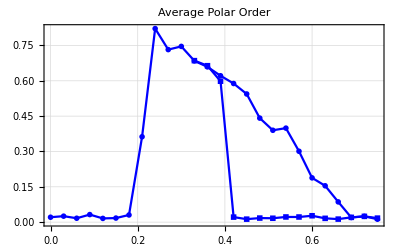

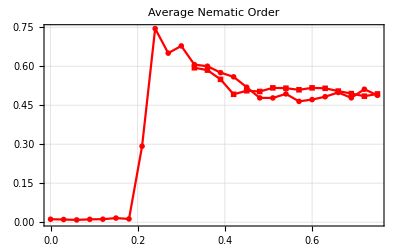

```mathematica
ListPlot[{porderforwards,porderbackwards},Joined->True,GridLines->Automatic,PlotLabel->Style["Average Polar Order",14],PlotRange->All,PlotMarkers->{Automatic,Medium},PlotStyle->Blue,Frame->True]
ListPlot[{norderforwards,norderbackwards},Joined->True,GridLines->Automatic,PlotLabel->Style["Average Nematic Order",14],PlotRange->All,PlotMarkers->{Automatic,Medium},PlotStyle->Red,Frame->True]
```

```mathematica
deltaP=Thread[{porderbackwards[[All,1]],-(porderbackwards[[;;,2]])+(porderforwards[[12;;,2]])}];
```

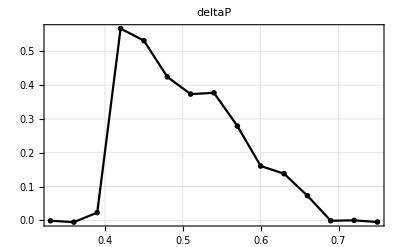

```mathematica
ListPlot[deltaP,Joined->True,GridLines->Automatic,PlotLabel->Style["deltaP",14],PlotRange->All,PlotMarkers->{Automatic,Medium},PlotStyle->Black,Frame->True]
```